```mathematica
ClearAll["Global`*"];
```

```mathematica
λ[k_]:=ℏ^2*k^2/(2*m);
M={{V0+λ[k-g]-ϵ,V1,V2},
{V1,V0+λ[k]-ϵ,V1},
{V2,V1,V0+λ[k+g]-ϵ}
};
```

```mathematica
M//MatrixForm
```

(V0-ϵ+((-g+k)^2 ℏ^2)/(2 m) | V1 | V2
V1 | V0-ϵ+(k^2 ℏ^2)/(2 m) | V1
V2 | V1 | V0-ϵ+((g+k)^2 ℏ^2)/(2 m))

```mathematica
Sols=Solve[Det[M]==0,ϵ]
```

{{ϵ→(6 m^3 V0+2 g^2 m^2 ℏ^2+3 k^2 m^2 ℏ^2)/(6 m^3)+(-384 m^6 V1^2-192 m^6 V2^2-16 g^4 m^4 ℏ^4-192 g^2 k^2 m^4 ℏ^4)/(12 2^(2/3) m^3 (-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6+√(4 (-384 m^6 V1^2-192 m^6 V2^2-16 g^4 m^4 ℏ^4-192 g^2 k^2 m^4 ℏ^4)^3+(-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6)^2))^(1/3))-1/(24 2^(1/3) m^3)(-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6+√(4 (-384 m^6 V1^2-192 m^6 V2^2-16 g^4 m^4 ℏ^4-192 g^2 k^2 m^4 ℏ^4)^3+(-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6)^2))^(1/3)},{ϵ→(6 m^3 V0+2 g^2 m^2 ℏ^2+3 k^2 m^2 ℏ^2)/(6 m^3)-((1+ⅈ √3) (-384 m^6 V1^2-192 m^6 V2^2-16 g^4 m^4 ℏ^4-192 g^2 k^2 m^4 ℏ^4))/(24 2^(2/3) m^3 (-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6+√(4 (-384 m^6 V1^2-192 m^6 V2^2-16 g^4 m^4 ℏ^4-192 g^2 k^2 m^4 ℏ^4)^3+(-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6)^2))^(1/3))+1/(48 2^(1/3) m^3)(1-ⅈ √3) (-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6+√(4 (-384 m^6 V1^2-192 m^6 V2^2-16 g^4 m^4 ℏ^4-192 g^2 k^2 m^4 ℏ^4)^3+(-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6)^2))^(1/3)},{ϵ→(6 m^3 V0+2 g^2 m^2 ℏ^2+3 k^2 m^2 ℏ^2)/(6 m^3)-((1-ⅈ √3) (-384 m^6 V1^2-192 m^6 V2^2-16 g^4 m^4 ℏ^4-192 g^2 k^2 m^4 ℏ^4))/(24 2^(2/3) m^3 (-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6+√(4 (-384 m^6 V1^2-192 m^6 V2^2-16 g^4 m^4 ℏ^4-192 g^2 k^2 m^4 ℏ^4)^3+(-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6)^2))^(1/3))+1/(48 2^(1/3) m^3)(1+ⅈ √3) (-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6+√(4 (-384 m^6 V1^2-192 m^6 V2^2-16 g^4 m^4 ℏ^4-192 g^2 k^2 m^4 ℏ^4)^3+(-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6)^2))^(1/3)}}

```mathematica
ϵ1=(6 m^3 V0+2 g^2 m^2 ℏ^2+3 k^2 m^2 ℏ^2)/(6 m^3)+(-384 m^6 V1^2-192 m^6 V2^2-16 g^4 m^4 ℏ^4-192 g^2 k^2 m^4 ℏ^4)/(12 2^(2/3) m^3 (-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6+√(4 (-384 m^6 V1^2-192 m^6 V2^2-16 g^4 m^4 ℏ^4-192 g^2 k^2 m^4 ℏ^4)^3+(-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6)^2))^(1/3))-1/(24 2^(1/3) m^3)(-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6+√(4 (-384 m^6 V1^2-192 m^6 V2^2-16 g^4 m^4 ℏ^4-192 g^2 k^2 m^4 ℏ^4)^3+(-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6)^2))^(1/3);
ϵ2=Re[(6 m^3 V0+2 g^2 m^2 ℏ^2+3 k^2 m^2 ℏ^2)/(6 m^3)-((1+ⅈ √3) (-384 m^6 V1^2-192 m^6 V2^2-16 g^4 m^4 ℏ^4-192 g^2 k^2 m^4 ℏ^4))/(24 2^(2/3) m^3 (-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6+√(4 (-384 m^6 V1^2-192 m^6 V2^2-16 g^4 m^4 ℏ^4-192 g^2 k^2 m^4 ℏ^4)^3+(-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6)^2))^(1/3))+1/(48 2^(1/3) m^3)(1-ⅈ √3) (-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6+√(4 (-384 m^6 V1^2-192 m^6 V2^2-16 g^4 m^4 ℏ^4-192 g^2 k^2 m^4 ℏ^4)^3+(-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6)^2))^(1/3)];
ϵ3=Re[(6 m^3 V0+2 g^2 m^2 ℏ^2+3 k^2 m^2 ℏ^2)/(6 m^3)-((1-ⅈ √3) (-384 m^6 V1^2-192 m^6 V2^2-16 g^4 m^4 ℏ^4-192 g^2 k^2 m^4 ℏ^4))/(24 2^(2/3) m^3 (-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6+√(4 (-384 m^6 V1^2-192 m^6 V2^2-16 g^4 m^4 ℏ^4-192 g^2 k^2 m^4 ℏ^4)^3+(-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6)^2))^(1/3))+1/(48 2^(1/3) m^3)(1+ⅈ √3) (-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6+√(4 (-384 m^6 V1^2-192 m^6 V2^2-16 g^4 m^4 ℏ^4-192 g^2 k^2 m^4 ℏ^4)^3+(-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6)^2))^(1/3)];
```

```mathematica
V0=0;V1=1;V2=1;ℏ=1;m=1/2;g=2*Pi;
```

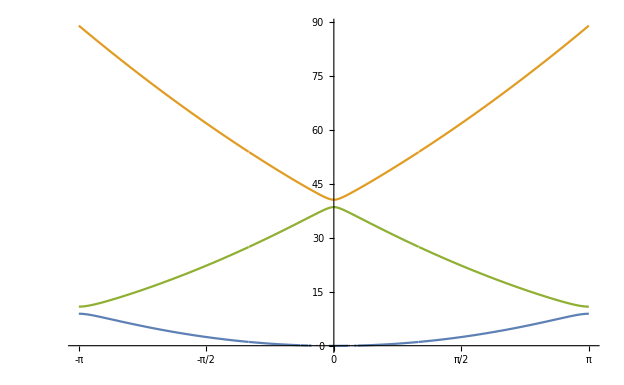

```mathematica
Plot[{ϵ1,ϵ2,ϵ3},{k,-Pi,Pi},Ticks->{Range[-Pi,Pi,Pi/4],Automatic}]
```

```mathematica
Simplify[-(-m V2-2 π^2 ℏ^2+v √(8 m^2 V1^2+(m V2+2 π^2 ℏ^2)^2))/(2 m)+(m V2+2 π^2 ℏ^2+√(8 m^2 V1^2+(m V2+2 π^2 ℏ^2)^2))/(2 m),Assumptions->{V1>0,V2>0}]
```

V2+(2 π^2 ℏ^2)/m

```mathematica
M={{V0+λ[k-g]-ϵ,V2},
{V2,V0+λ[k+g]-ϵ}
};
```

```mathematica
M//MatrixForm
```

(-ϵ+(2 π^2 ℏ^2)/m | V2
V2 | -ϵ+(2 π^2 ℏ^2)/m)

```mathematica
Solve[Det[M]==0,ϵ]
```

{{ϵ→(-m V2+2 π^2 ℏ^2)/m},{ϵ→(m V2+2 π^2 ℏ^2)/m}}

```mathematica
Simplify[(-m V2+2 π^2 ℏ^2)/m-(m V2+2 π^2 ℏ^2)/m]
```

-2 V2

```mathematica
ϵ1=(6 m^3 V0+2 g^2 m^2 ℏ^2+3 k^2 m^2 ℏ^2)/(6 m^3)+(-384 m^6 V1^2-192 m^6 V2^2-16 g^4 m^4 ℏ^4-192 g^2 k^2 m^4 ℏ^4)/(12 2^(2/3) m^3 (-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6+√(4 (-384 m^6 V1^2-192 m^6 V2^2-16 g^4 m^4 ℏ^4-192 g^2 k^2 m^4 ℏ^4)^3+(-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6)^2))^(1/3))-1/(24 2^(1/3) m^3)(-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6+√(4 (-384 m^6 V1^2-192 m^6 V2^2-16 g^4 m^4 ℏ^4-192 g^2 k^2 m^4 ℏ^4)^3+(-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6)^2))^(1/3);
ϵ2=Im[(6 m^3 V0+2 g^2 m^2 ℏ^2+3 k^2 m^2 ℏ^2)/(6 m^3)-((1+ⅈ √3) (-384 m^6 V1^2-192 m^6 V2^2-16 g^4 m^4 ℏ^4-192 g^2 k^2 m^4 ℏ^4))/(24 2^(2/3) m^3 (-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6+√(4 (-384 m^6 V1^2-192 m^6 V2^2-16 g^4 m^4 ℏ^4-192 g^2 k^2 m^4 ℏ^4)^3+(-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6)^2))^(1/3))+1/(48 2^(1/3) m^3)(1-ⅈ √3) (-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6+√(4 (-384 m^6 V1^2-192 m^6 V2^2-16 g^4 m^4 ℏ^4-192 g^2 k^2 m^4 ℏ^4)^3+(-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6)^2))^(1/3)];
ϵ3=Im[(6 m^3 V0+2 g^2 m^2 ℏ^2+3 k^2 m^2 ℏ^2)/(6 m^3)-((1-ⅈ √3) (-384 m^6 V1^2-192 m^6 V2^2-16 g^4 m^4 ℏ^4-192 g^2 k^2 m^4 ℏ^4))/(24 2^(2/3) m^3 (-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6+√(4 (-384 m^6 V1^2-192 m^6 V2^2-16 g^4 m^4 ℏ^4-192 g^2 k^2 m^4 ℏ^4)^3+(-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6)^2))^(1/3))+1/(48 2^(1/3) m^3)(1+ⅈ √3) (-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6+√(4 (-384 m^6 V1^2-192 m^6 V2^2-16 g^4 m^4 ℏ^4-192 g^2 k^2 m^4 ℏ^4)^3+(-27648 m^9 V1^2 V2+4608 g^2 m^8 V1^2 ℏ^2-4608 g^2 m^8 V2^2 ℏ^2+128 g^6 m^6 ℏ^6-4608 g^4 k^2 m^6 ℏ^6)^2))^(1/3)];
```

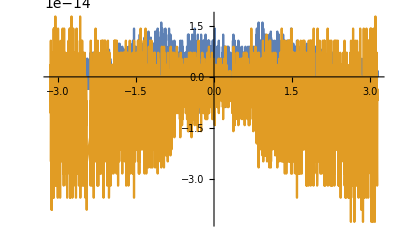

```mathematica
Plot[{ϵ2,ϵ3},{k,-Pi,Pi}]
```